```mathematica
Clear["Global`*"];
```

```mathematica
<</home/xierr/.Mathematica/Applications/CustomTicks/CustomTicks.m
```

```mathematica
tlen=0.014;tickd=In;thick=Thickness[0.002];ip={{80,30},{60,30}};
```

```mathematica
lambda[g_Graph,n_]:=Module[{degrees},degrees=VertexDegree[g];Eigenvalues[IdentityMatrix[n]-(AdjacencyMatrix[g]/Sqrt[Outer[Times,N[degrees],N[degrees]]])]]
```

```mathematica
P[s_,β_]:=(1+β)Gamma[(β+2)/(β+1)]^(β+1)s^β Exp[-Gamma[(β+2)/(β+1)]^(β+1)s^(β+1)];
```

```mathematica
ξsb[ξb_?NumericQ]:=Gamma[ξb+1/2]/Gamma[ξb];
NV[L_?NumericQ,ξb_?NumericQ, f_?NumericQ]:= (1-f)L+((ξsb[ξb]/(√ξb))^-2-1) (L/f)^2;
```

```mathematica
Sigma[data_List,l_]:=N[(Length[data]-1)/Length[data] Variance[BinCounts[data,Append[{-l,l}+MinMax[data],l]]]]
```

```mathematica
cliprange[points_List,xmax_]:=Module[{xmaxpos},xmaxpos=Position[points,Nearest[points[[All,1]],xmax][[1]]][[1,1]];
points[[1;;xmaxpos]]];
```

#### Unweighted

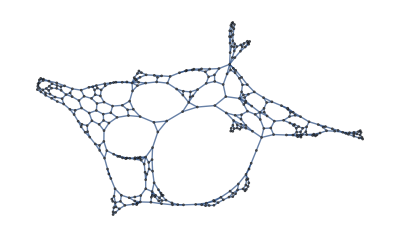

```mathematica
temp1=Import["/home/xierr/Desktop/pato_all/pato_new_all/pato_complex_network/PSAdj/Pp_M_Tokyo_U_N_26h_1.csv","Data"][[All,{1,2}]]/.{x_,y_}:>{IntegerPart[x],IntegerPart[y]};
SA1=SparseArray[(#->1)&/@Join[temp1,Reverse[#]&/@temp1]];
G1=AdjacencyGraph[SA1]
n1=VertexCount[G1];
LaunchKernels[4];
DistributeDefinitions[lambda];
eigens1=lambda[G1,n1];
cumuhistdata1=Transpose[{MovingAverage[#[[1]],2],#[[2]]}&@HistogramList[eigens1,100,"CDF"]];
m1=30;Nbar1[x_]=Fit[cumuhistdata1,{1,Sequence@@Table[x^i,{i,1,m1}]},x];
nnd1=Transpose[{MovingAverage[#[[1]],2],#[[2]]}&@HistogramList[Abs[Differences[n1 Nbar1[Sort[eigens1]]]],50,"PDF"]];
nnd1=cliprange[nnd1,4];
nlmNND1=NonlinearModelFit[Select[nnd1,#[[1]]≥0&],P[s,β],{β},s];
beta1=N[nlmNND1["BestFitParameters"][[1,2]]];
unfoldlamb1=Sort[Flatten[n1 Nbar1[eigens1]]];
nv1=Table[{l,Sigma[unfoldlamb1,l]},{l,0.1,20,0.1}];
nlmNV1=NonlinearModelFit[nv1,NV[L,ξb,f],{ξb,f},L];
f1=N[nlmNV1["BestFitParameters"][[2,2]]];
xi1=N[nlmNV1["BestFitParameters"][[1,2]]];
```

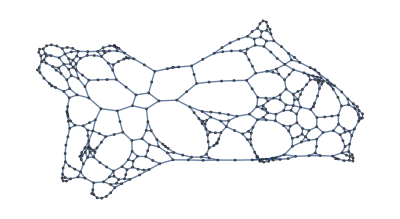

```mathematica
temp2=Import["/home/xierr/Desktop/pato_all/pato_new_all/pato_complex_network/PSAdj/Pv_L_I+4xR_Fc_N_155d_3.csv","Data"][[All,{1,2}]]/.{x_,y_}:>{IntegerPart[x],IntegerPart[y]};
SA2=SparseArray[(#->1)&/@Join[temp2,Reverse[#]&/@temp2]];
G2=AdjacencyGraph[SA2]
n2=VertexCount[G2];
LaunchKernels[4];
DistributeDefinitions[lambda];
eigens2=lambda[G2,n2];
cumuhistdata2=Transpose[{MovingAverage[#[[1]],2],#[[2]]}&@HistogramList[eigens2,100,"CDF"]];
m2=30;Nbar2[x_]=Fit[cumuhistdata2,{1,Sequence@@Table[x^i,{i,1,m2}]},x];
nnd2=Transpose[{MovingAverage[#[[1]],2],#[[2]]}&@HistogramList[Abs[Differences[n2 Nbar2[Sort[eigens2]]]],100,"PDF"]];
nnd2=cliprange[nnd2,4];
nlmNND2=NonlinearModelFit[Select[nnd2,#[[1]]≥0&],P[s,β],{β},s];
beta2=N[nlmNND2["BestFitParameters"][[1,2]]];
unfoldlamb2=Sort[Flatten[n2 Nbar2[eigens2]]];
nv2=Table[{l,Sigma[unfoldlamb2,l]},{l,0.1,20,0.1}];
nlmNV2=NonlinearModelFit[nv2,NV[L,ξb,f],{ξb,f},L];
f2=N[nlmNV2["BestFitParameters"][[2,2]]];
xi2=N[nlmNV2["BestFitParameters"][[1,2]]];
```

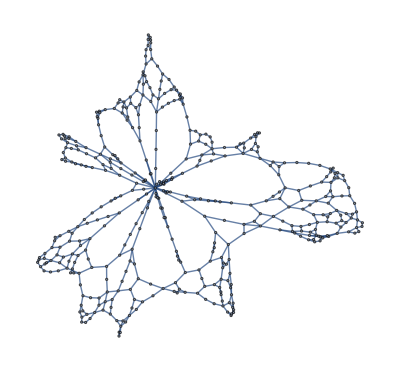

```mathematica
temp3=Import["/home/xierr/Desktop/pato_all/pato_new_all/pato_complex_network/PSAdj/Rb_M_I_U_N_31d_2.csv","Data"][[All,{1,2}]]/.{x_,y_}:>{IntegerPart[x],IntegerPart[y]};
SA3=SparseArray[(#->1)&/@Join[temp3,Reverse[#]&/@temp3]];
G3=AdjacencyGraph[SA3]
n3=VertexCount[G3];
LaunchKernels[4];
DistributeDefinitions[lambda];
eigens3=lambda[G3,n3];
cumuhistdata3=Transpose[{MovingAverage[#[[1]],2],#[[2]]}&@HistogramList[eigens3,100,"CDF"]];
m3=30;Nbar3[x_]=Fit[cumuhistdata3,{1,Sequence@@Table[x^i,{i,1,m3}]},x];
nnd3=Transpose[{MovingAverage[#[[1]],2],#[[2]]}&@HistogramList[Abs[Differences[n3 Nbar3[Sort[eigens3]]]],50,"PDF"]];
nnd3=cliprange[nnd3,4];
nlmNND3=NonlinearModelFit[Select[nnd3,#[[1]]≥0&],P[s,β],{β},s];
beta3=N[nlmNND3["BestFitParameters"][[1,2]]];
unfoldlamb3=Sort[Flatten[n3 Nbar3[eigens3]]];
nv3=Table[{l,Sigma[unfoldlamb3,l]},{l,0.1,20,0.1}];
nlmNV3=NonlinearModelFit[nv3,NV[L,ξb,f],{ξb,f},L];
f3=N[nlmNV3["BestFitParameters"][[2,2]]];
xi3=N[nlmNV3["BestFitParameters"][[1,2]]];
```

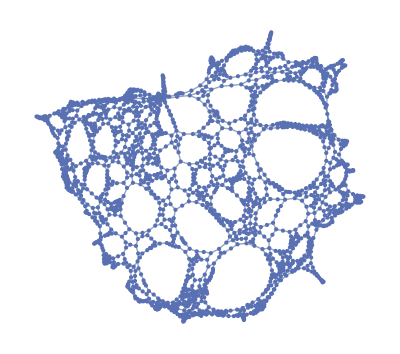

```mathematica
temp4=Import["/home/xierr/Desktop/pato_all/pato_new_all/pato_complex_network/PSAdj/Ag_M_I+4R_U_N_42d_1.csv","Data"][[All,{1,2}]]/.{x_,y_}:>{IntegerPart[x],IntegerPart[y]};
SA4=SparseArray[(#->1)&/@Join[temp4,Reverse[#]&/@temp4]];
G4=AdjacencyGraph[SA4]
n4=VertexCount[G4];
LaunchKernels[4];
DistributeDefinitions[lambda];
eigens4=lambda[G4,n4];
cumuhistdata4=Transpose[{MovingAverage[#[[1]],2],#[[2]]}&@HistogramList[eigens4,100,"CDF"]];
m4=30;Nbar4[x_]=Fit[cumuhistdata4,{1,Sequence@@Table[x^i,{i,1,m4}]},x];
nnd4=Transpose[{MovingAverage[#[[1]],2],#[[2]]}&@HistogramList[Abs[Differences[n4 Nbar4[Sort[eigens4]]]],100,"PDF"]];
nnd4=cliprange[nnd4,4];
nlmNND4=NonlinearModelFit[Select[nnd4,#[[1]]≥0&],P[s,β],{β},s];
beta4=N[nlmNND4["BestFitParameters"][[1,2]]];
unfoldlamb4=Sort[Flatten[n4 Nbar4[eigens4]]];
nv4=Table[{l,Sigma[unfoldlamb4,l]},{l,0.1,35,0.1}];
nlmNV4=NonlinearModelFit[nv4,NV[L,ξb,f],{ξb,f},L];
f4=N[nlmNV4["BestFitParameters"][[2,2]]];
xi4=N[nlmNV4["BestFitParameters"][[1,2]]];
```

```mathematica
beta4
```

0.487031

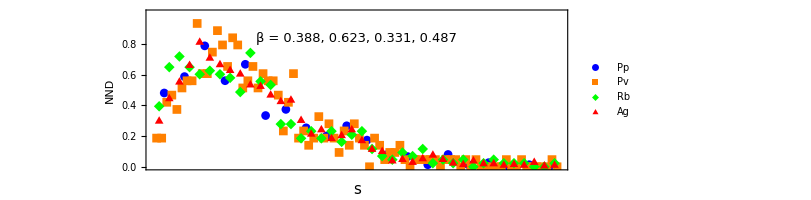

```mathematica
nndpoints=ListPlot[{nnd1,nnd2,nnd3,nnd4}(*use your data*),PlotRange->{{0,4},{0,1}},DataRange->{{0,4},{0,1}},AspectRatio->1/3.(*specify the height-to-width ratio*),ImageSize->600,PlotMarkers->Automatic,Frame->True,PlotStyle->{Blue, Orange, Green, Red},
(*********************Frame Ticks***********************)
ImagePadding->ip,PlotRangeClipping->False,FrameStyle->Directive[thick,Black,FontSize->20,FontFamily->"Times New Roman"],FrameTicksStyle->Directive[thick,"Label", 15],FrameTicks->{{LinTicks[{0,0.2,0.4,0.6,0.8},{0.1,0.3,0.5,0.7,0.9},MajorTickLength->2tlen,MinorTickLength->tlen,ShowFirst->True,TickDirection->tickd],(*left*)
LinTicks[{0,0.2,0.4,0.6,0.8},{0.1,0.3,0.5,0.7,0.9},MajorTickLength->2tlen,MinorTickLength->tlen,ShowFirst->False,TickDirection->tickd,ShowTickLabels->False]},(*right*){LinTicks[{0,1,2,3,4},{0.5,1.5,2.5,3.5},MajorTickLength->2tlen,MinorTickLength->tlen,TickDirection->tickd,ShowTickLabels->False],(*down*)
LinTicks[{0,1,2,3,4},{0.5,1.5,2.5,3.5},MajorTickLength->2tlen,MinorTickLength->tlen,TickDirection->tickd,ShowTickLabels->True]}},(*up*)FrameLabel->{None,Style["NND",FontFamily->"Times New Roman",15]},
(***************************************)PlotLegends->Placed[PointLegend[Automatic,Style[#,10,FontFamily->"Times New Roman"]&/@{"Pp","Pv","Rb","Ag"},LegendFunction->Framed,LegendMargins->0],{(*legend position*)Scaled[0.85],Scaled[0.5]}],Epilog->{Text[Style["  β = 0.388, 0.623, 0.331, 0.487",FontSize->13,FontFamily->"Times New Roman"],Scaled[{0.5,0.82}]],Text[Style["StyleBox[\"s\",FontSlant->\"Italic\"]",FontSize->15,FontFamily->"Times New Roman"],Scaled[{0.5,-0.12}]]}]
```

```mathematica
clippoints = Table[{s,Normal[nlmNND1]},{s,0.0001,4,0.04}] ;
nndmat=ListStepPlot[clippoints,Center,AxesOrigin->{0,0},PlotRange->{{0,4},{0,1}},PlotStyle->Lighter[Black],Frame->True];
```

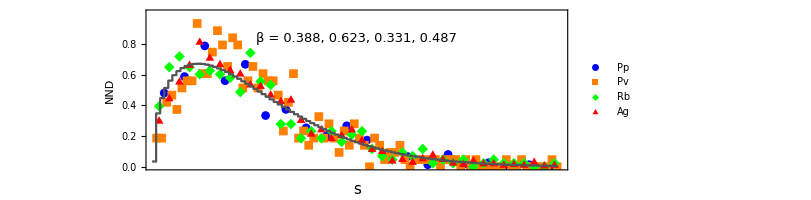

```mathematica
p1=Show[nndpoints,nndmat]
```

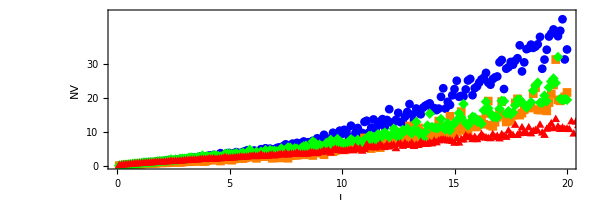

```mathematica
nvpoints=ListPlot[{nv1,nv2,nv3,nv4}(*use your data*),PlotRange->{{0,20},{0,45}},DataRange->{{0,20},{0,45}},AspectRatio->1/3.(*specify the height-to-width ratio*),ImageSize->600,PlotMarkers->Automatic,Frame->True,PlotStyle->{Blue, Orange, Green, Red},
(*********************Frame Ticks***********************)
ImagePadding->ip,FrameStyle->Directive[thick,Black,FontSize->20,FontFamily->"Times New Roman"],FrameTicksStyle->Directive[thick,"Label", 15],FrameTicks->{{LinTicks[Range[0,40,10],Range[5,45,10],MajorTickLength->2tlen,MinorTickLength->tlen,ShowFirst->True,ShowLast->False,TickDirection->tickd],(*left*)
LinTicks[Range[0,40,10],Range[5,45,10],MajorTickLength->2tlen,MinorTickLength->tlen,ShowFirst->False,TickDirection->tickd,ShowTickLabels->False]},(*right*){LinTicks[Range[0,20,5],Range[2.5,17.5,5],MajorTickLength->2tlen,MinorTickLength->tlen,TickDirection->tickd,ShowTickLabels->True],(*down*)
LinTicks[Range[0,20,5],Range[2.5,17.5,5],MajorTickLength->2tlen,MinorTickLength->tlen,TickDirection->tickd,ShowTickLabels->False]}},(*up*)FrameLabel->{Style["StyleBox[\"L\",FontSlant->\"Italic\"]",FontSize->15,FontFamily->"Times New Roman"],Style["NV",FontFamily->"Times New Roman",15]}]
```

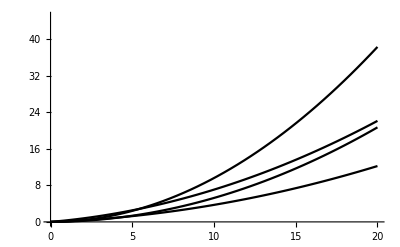

```mathematica
nvcurv=Plot[{Normal[nlmNV1],Normal[nlmNV2],Normal[nlmNV3],Normal[nlmNV4]},{L,0,20},PlotStyle->Black,PlotRange->{{0,20},{0,45}}]
(*nvcurv=Plot[Normal[nlmNV3],{L,0,12.5},PlotStyle->Black,PlotRange->{{0,12.5},{0,15}}]*)
```

```mathematica
xi4
```

14.0495

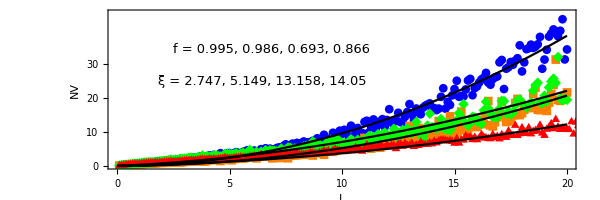

```mathematica
p3=Show[nvpoints,nvcurv,(*we want nvcurv as background*)Epilog->{Text[Style["StyleBox[\"f\",FontSlant->\"Italic\"] = 0.995, 0.986, 0.693, 0.866",FontSize->13,FontFamily->"Times New Roman"],Scaled[{0.35,0.75}]],Text[Style["\!\(\*OverscriptBox[\(ξ\), \(_\)]\) = 2.747, 5.149, 13.158, 14.05",FontSize->13,FontFamily->"Times New Roman"],Scaled[{0.33,0.55}]]}]
```

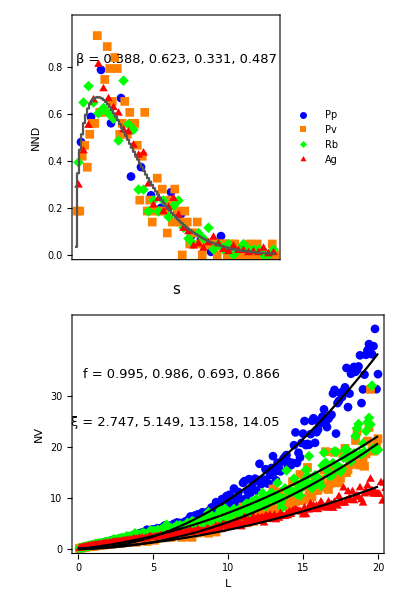

```mathematica
fig=Column[{p1,p3},,Spacings->-3.5]
```

```mathematica
Export["fungal_net.jpg",fig]
```

fungal_net.jpg